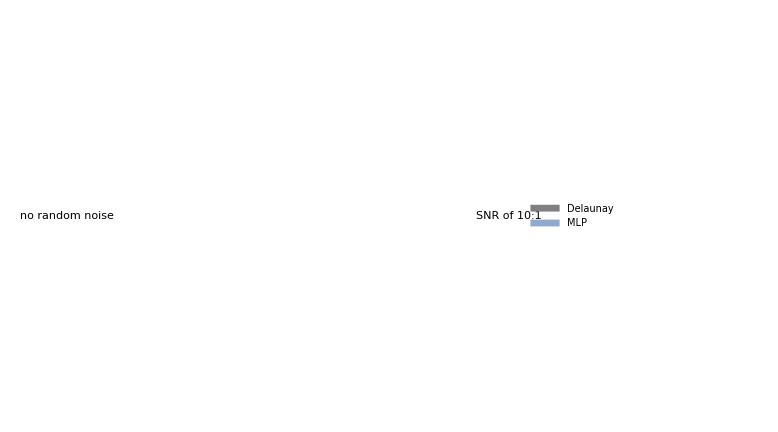

-Graphics-

```mathematica
(* Generate box chart for analytic test function. *)
ratio=1;

d02=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/DelaunayP1-0.00-oscillatory-2.csv"];
m02=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/NeuralNetwork-0.00-oscillatory-2.csv"];
d12=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/DelaunayP1-0.10-oscillatory-2.csv"];
m12=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/NeuralNetwork-0.10-oscillatory-2.csv"];

d020=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/DelaunayP1-0.00-oscillatory-20.csv"];
m020=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/NeuralNetwork-0.00-oscillatory-20.csv"];
d120=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/DelaunayP1-0.10-oscillatory-20.csv"];
m120=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Analytic/NeuralNetwork-0.10-oscillatory-20.csv"];

labels2=d02[[2;;-1,1]];
labels20=d020[[2;;-1,1]];

noNoise2=Transpose[{d02,m02}[[1;;-1,2;;-1,2;;-1]],1<->2];
yesNoise2=Transpose[{d12,m12}[[1;;-1,2;;-1,2;;-1]],1<->2];

noNoise20=Transpose[{d020,m020[[2;;-1]]}[[1;;-1,2;;-1,2;;-1]],1<->2];
yesNoise20=Transpose[{d120,m120[[2;;-1]]}[[1;;-1,2;;-1,2;;-1]],1<->2];

p1=Legended[GraphicsGrid[{{
Labeled[BoxWhiskerChart[noNoise2,{{"MedianNotch"},{"Outliers",None,Gray}},BarOrigin->Bottom,ScalingFunctions->"Log",
 PlotRange->{All,{-12,-2.5}},ChartStyle->{Gray,RGBColor[144/256,171/256,206/256]},PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->{labels2,{"",""}},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageSize->270,BarSpacing->{.1,.9}],"no random noise",Top,LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageMargins->5],
Labeled[BoxWhiskerChart[yesNoise2,{{"MedianNotch"},{"Outliers",None,Gray}},BarOrigin->Bottom,ScalingFunctions->"Log",
 PlotRange->{All,{-12,-2.5}},ChartStyle->{Gray,RGBColor[144/256,171/256,206/256]},PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->{labels2,{"",""}},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageSize->270,BarSpacing->{.1,.9}],"SNR of 10:1",Top,LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageMargins->5]
}},PlotRangePadding->0,ImageSize->Large,Spacings->-30],Placed[SwatchLegend[{Gray,RGBColor[144/256,171/256,206/256]},{"Delaunay","MLP"},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},LegendLayout->"Row",Spacings->{.5,2.2},LegendMargins->0],{{.5,1.02},Top}]]

p2=Legended[GraphicsGrid[{{
Labeled[BoxWhiskerChart[noNoise20,{{"MedianNotch"},{"Outliers",None,Gray}},BarOrigin->Bottom,ScalingFunctions->"Log",
 PlotRange->{All,{-6.3,-.5}},ChartStyle->{Gray,RGBColor[144/256,171/256,206/256]},PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->{labels20,{"",""}},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageSize->270,BarSpacing->{.1,.9}],"no random noise",Top,LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageMargins->5],
Labeled[BoxWhiskerChart[yesNoise20,{{"MedianNotch"},{"Outliers",None,Gray}},BarOrigin->Bottom,ScalingFunctions->"Log",
 PlotRange->{All,{-6.3,-.5}},ChartStyle->{Gray,RGBColor[144/256,171/256,206/256]},PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->{labels20,{"",""}},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageSize->270,BarSpacing->{.1,.9}],"SNR of 10:1",Top,LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageMargins->5]
}},PlotRangePadding->0,ImageSize->Large,Spacings->-30],Placed[SwatchLegend[{Gray,RGBColor[144/256,171/256,206/256]},{"Delaunay","MLP"},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},LegendLayout->"Row",Spacings->{.5,2.2},LegendMargins->0],{{.5,1.02},Top}]]

Export["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/convergence-2d.pdf",p1];
Export["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/convergence-20d.pdf",p2];
```

{0.0689603,0.0251364,0.00669474,0.00169715,0.000563151,0.000137246}

{0.612794,0.459841,0.423351,0.395305}

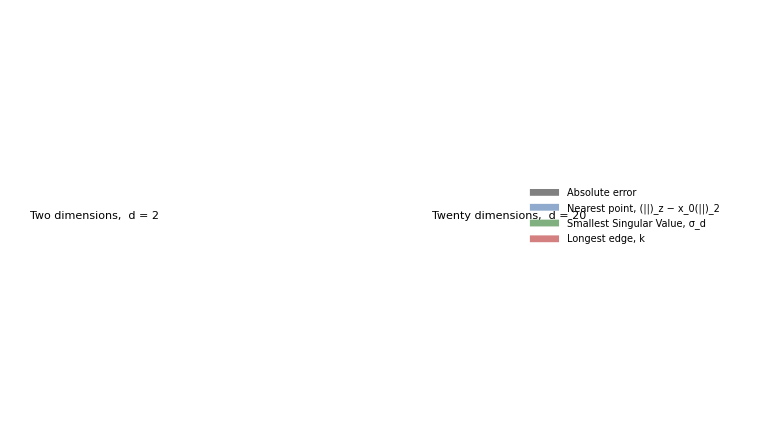

```mathematica
(* Generate box chart for analytic test function that shows spacing. *)
ratio=1;

d2e=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-abs_error-oscillatory-2D-1000N.csv"];
d2n=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-nearest_vertex-oscillatory-2D-1000N.csv"];
d2s=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-smallest_sv-oscillatory-2D-1000N.csv"];
d2l=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-longest_edge-oscillatory-2D-1000N.csv"];

d20e=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-abs_error-oscillatory-20D-1000N.csv"];
d20n=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-nearest_vertex-oscillatory-20D-1000N.csv"];
d20s=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-smallest_sv-oscillatory-20D-1000N.csv"];
d20l=Import["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/Data/Analytic/Delaunay-longest_edge-oscillatory-20D-1000N.csv"];

labels2=d2l[[2;;-1,1]];
labels20=d20l[[2;;-1,1]];

maxErr2=Max/@d2e[[2;;-1,2;;-1]]
maxErr20=Max/@d20e[[3;;-1,2;;-1]]

twoD=Transpose[{d2e,d2n,d2s,d2l}[[1;;-1,2;;-1,2;;-1]],1<->2];
twentyD=Transpose[{d20e,d20n,d20s,d20l}[[1;;-1,2;;-1,2;;-1]],1<->2];

colors={Gray,RGBColor[144/256,171/256,206/256],RGBColor[0.5,0.69,0.5],RGBColor[0.83,0.5,0.5]};
p1=Legended[GraphicsGrid[{{
Labeled[BoxWhiskerChart[twoD,{{"MedianNotch"},{"Outliers",None,Gray}},BarOrigin->Bottom,ScalingFunctions->"Log",
 PlotRange->{All,{-12,1}},ChartStyle->colors,PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->{labels2,{"",""}},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageSize->270,BarSpacing->{.1,1.5}],
"Two dimensions,  d = 2",Top,LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageMargins->5],
Labeled[BoxWhiskerChart[twentyD,{{"MedianNotch"},{"Outliers",None,Gray}},BarOrigin->Bottom,ScalingFunctions->"Log",
 PlotRange->{All,{-12,1}},ChartStyle->colors,PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->{labels20,{"",""}},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageSize->270,BarSpacing->{.1,1.5}],
"Twenty dimensions,  d = 20",Top,LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},ImageMargins->5]
}},PlotRangePadding->0,ImageSize->Large,Spacings->-30],Placed[SwatchLegend[colors,{"Absolute error                      ", "Nearest point,  (||)_z − x_0(||)_2","Smallest Singular Value, σ_d", "Longest edge,  k"},LabelStyle->{FontSize->13,FontFamily->"Liberation Serif",FontColor->Black},LegendLayout->"Row",Spacings->{.3,1.2},LegendMargins->{{30,0},{7,0}}],{{.5,1.02},Top}]]

Export["/Users/thomaslux/Git/papers/[2019-02]_NUMA_(interpolant_error_bound)/theorem-convergence.pdf",p1];
```

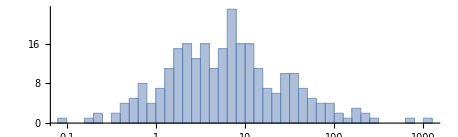

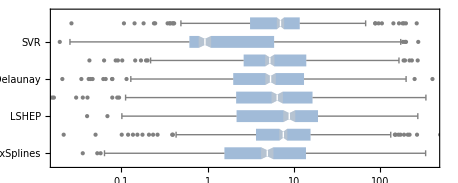

```mathematica
(* Generate histogram for Forest Fire data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/data_forestfires_area.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/absolute_error_results_forestfires.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
ScalingFunctions->"Log", PlotRange->{{-4,6},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

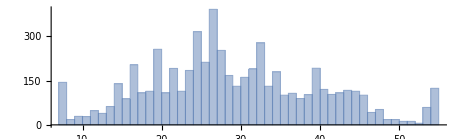

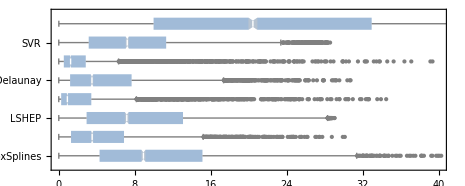

```mathematica
(* Generate histogram for Parkinsons data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/data_parkinsons_updrs_total_UPDRS.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},50,PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/absolute_error_results_parkinsons_updrs.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
 PlotRange->{{0,40},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

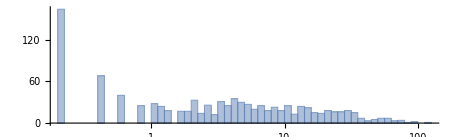

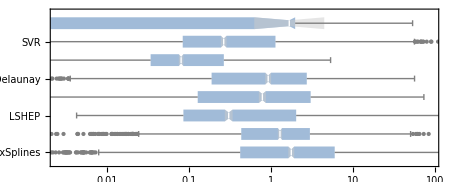

```mathematica
(* Generate histogram for Sydney, Australia Daily Rainfall data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/data_weatherAUS_RainfallTomorrow.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/absolute_error_results_weatherAUS.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
ScalingFunctions->"Log", PlotRange->{{-6,4.5},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

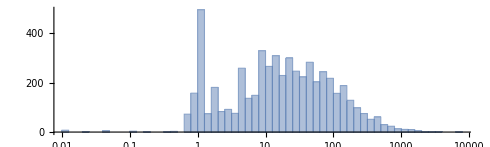

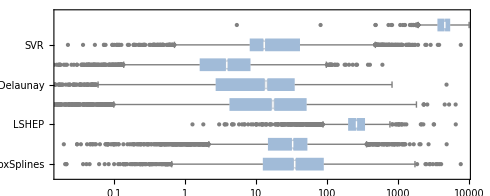

```mathematica
(* Generate histogram for Credit Card Transaction data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/data_creditcard_Amount.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/absolute_error_results_creditcard.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
ScalingFunctions->"Log", PlotRange->{{-4,9},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

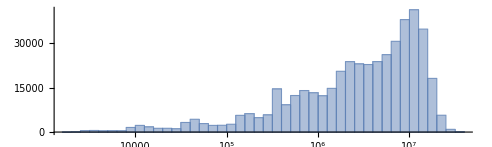

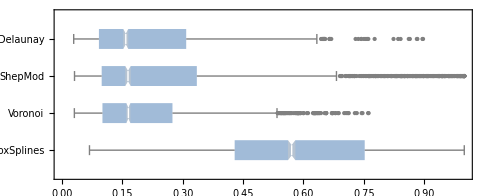

```mathematica
(* Generate histogram for I/O Zone Throughput data *)

raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/data_iozone_150_Throughput.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/absolute_error_results_iozone_150.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},
 PlotRange->{{0,1},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,BarOrigin->Left,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

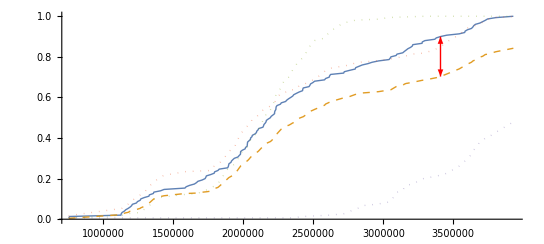

```mathematica
(* Generate Delaunay Example Prediction Plot *)
sample=Import["/Users/thomaslux/Git/VarSys/Paper_[2018-02-16]_IEEESE/Results/Delaunay_Example_Prediction.csv"];
trueConfig=sample[[1,3;;6]];
trueValues=Sort[sample[[1,7;;-1]]];
trueDist=Interpolation[Transpose[{trueValues,CDF[EmpiricalDistribution[trueValues],trueValues]}],InterpolationOrder->1];
sourceConfigs={};
sourceDists={Transpose[{trueValues,trueDist[trueValues]}]};
AppendTo[sourceDists,Transpose[{trueValues,sample[[-1,7;;-1]]}]];
For[i=2,i≤Length[sample]-1,i+=1,{
AppendTo[sourceConfigs,sample[[i,3;;6]]];
sourceValues=sample[[i,7;;-1]];
minVal=Min[sourceValues];
maxVal=Max[sourceValues];
f=Interpolation[Transpose[{sourceValues,CDF[EmpiricalDistribution[sourceValues],sourceValues]}],InterpolationOrder->1];
AppendTo[sourceDists,Transpose[{trueValues,f[Clip[trueValues,{minVal,maxVal}]]}]];
}]
opac=0.5;
ratio=.45;
aSize=.02;
Show[ListLinePlot[sourceDists,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black},PlotStyle->{Thick,{Thick,Dashed},{Thick,Dotted,Opacity[opac]},{Thick,Dotted,Opacity[opac]},{Thick,Dotted,Opacity[opac]}},AspectRatio->ratio],Graphics[{Red,Thick,Arrowheads[{-aSize,aSize}],Arrow[{{3408768.28,0.70306},{3408768,0.89933}}]}]]
```

Shape of subdata: {3016}

Min and Max:      0.0679302  1.

Shape of subdata: {3016}

Min and Max:      0.0286901  0.897434

Shape of subdata: {3016}

Min and Max:      0.0307091  1.

Shape of subdata: {3016}

Min and Max:      0.0303205  0.762108

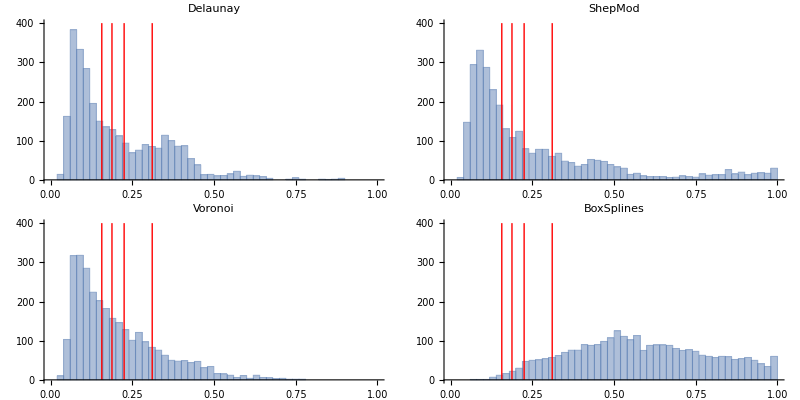

```mathematica
(* Distribution of performance by algorithm *)
(* KS Stats to P Values (for comparing two sets of 150 samples) *)
(*   0.1568      0.05    *)
(*   0.1879      0.01    *)
(*   0.2251      0.001   *)
(*   0.3110      1.0e-6  *)
(* Functions for extracting rows from data based on values in certain columns *)
data=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_NUMA/Data/Results/absolute_error_results_iozone_150.csv"];
colNames=data[[1]];
algCol=Position[colNames,"Algorithm"][[1,1]];
algNames=Union[data[[All,algCol]]][[2;;-1]];
ksValues={0.1568,0.1879,0.2251,0.3110};
dataByVal[col_,vals_,d_:data]:={
select[row_]:=Length[Position[vals,row[[col]]]]>0;
Select[d,select]
}[[1]][[1,2;;-1]];
dataByAlg[alg_,d_:data]:=dataByVal[algCol,{alg},d];

plots={};
ratio=0.5;
For[i=1,i≤Length[algNames],i+=1,{
subdata=dataByAlg[algNames[[i]]];
Print["Shape of subdata: ",Dimensions[subdata]];
Print["Min and Max:      ",Min[subdata],"  ",Max[subdata]];
hist=Show[Histogram[{{},subdata},{0,1,1/50},PlotLabel->algNames[[i]],PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}],
(*GridLines->{{{0.1568,Directive[Opacity[1.],Thick,Red]},
		{0.1879,Directive[Opacity[1.],Thick,Red]},
		{0.2251,Directive[Opacity[1.],Thick,Red]},
		{0.3110,Directive[Opacity[1.],Thick,Red]}},None}*)
Graphics[{Red,Thick,Line[{{0.1568,0},{0.1568,400}}]}],
Graphics[{Red,Thick,Line[{{0.1879,0},{0.1879,400}}]}],
Graphics[{Red,Thick,Line[{{0.2251,0},{0.2251,400}}]}],
Graphics[{Red,Thick,Line[{{0.3110,0},{0.3110,400}}]}]];
AppendTo[plots,hist];
}]
GraphicsGrid[{{plots[[2]],plots[[3]]},{plots[[4]],plots[[1]]}},
Spacings->0,AspectRatio->1/GoldenRatio]
```